```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]~StringJoin~".."]
```

H:\2_Projects\physics\5d_flavourful_axion

```mathematica
<<"WarpFlavourAxion`"
```

```mathematica
<<"MaTeX`"
```

```mathematica
<<"CustomTicks`"
```

#### Exact and approximate axion profile

```mathematica
$Assumptions={z>0,zIR>0,g>0,Δ>0,σ0>0};
```

```mathematica
(* 
g = g5 Sqrt[k];
σ = σ0 / (k zIR)^Δ = σ0 / zIR^Δ
*)
```

Exact axion profile without the normalization

```mathematica
a[z_,σ0_,Δ_,zIR_:10^8,g_:1]:=(z/zIR) ((g σ0)/(2Δ))^(1/Δ)(-BesselI[(Δ-1)/Δ,(g σ0)/Δ]/BesselI[-(Δ-1)/Δ,(g σ0)/Δ] BesselI[1/Δ,(g σ0)/Δ(z/zIR)^Δ]+BesselI[-1/Δ,(g σ0)/Δ(z/zIR)^Δ] )
```

```mathematica
aApprox[z_,σ0_,Δ_,zIR_:10^8,g_:1]:=(z/zIR) ((g σ0)/(2Δ))^(1/Δ)(-BesselI[(Δ-1)/Δ,(g σ0)/Δ]/BesselI[-(Δ-1)/Δ,(g σ0)/Δ] 1/Gamma[(Δ+1)/Δ]((g σ0)/(2Δ))^(1/Δ)z/zIR+1/Gamma[(Δ-1)/Δ]((g σ0)/(2Δ))^(-1/Δ)zIR/z)
```

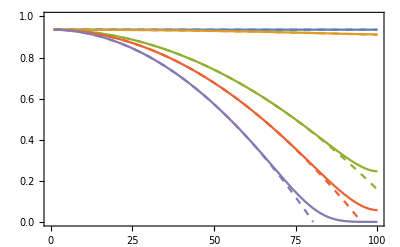

```mathematica
With[
{Δ=10,zIR=100},
Show[
Plot[Evaluate[a[z,#,Δ,zIR]&/@{0.1,1,10,20,100}],{z,1,zIR},PlotRange->{0,1},Frame->True],
Plot[Evaluate[aApprox[z,#,Δ,zIR]&/@{0.1,1,10,20,100}],{z,1,zIR},PlotRange->{0,1},Frame->True,PlotStyle->Dashed]
]
]
```

The non-flat contribution f_a^(0, 1) without the normalization

```mathematica
a01[z_,σ0_,Δ_,zIR_:10^8,g_:1]:=-a[z,σ0,Δ,zIR,g]+a[1,σ0,Δ,zIR,g]
```

```mathematica
aApprox01[z_,σ0_,Δ_,zIR_:10^8,g_:1]:=(-aApprox[z,σ0,Δ,zIR,g]+aApprox[1,σ0,Δ,zIR,g])//Simplify
```

```mathematica
aApprox01[z, σ0, Δ, zIR, g]
```

(4^(-1/Δ) (-1+z^2) ((g σ0)/Δ)^(2/Δ) BesselI[(-1+Δ)/Δ,(g σ0)/Δ])/(zIR^2 BesselI[-1+1/Δ,(g σ0)/Δ] Gamma[1+1/Δ])

The approximation used for small values of σ0

```mathematica
aApprox01Original[z_,σ0_,Δ_,zIR_:10^8,g_:1]:=-zIR/σ0 Sqrt[Δ-1] (g^2 σ0^2)/(4Δ(Δ-1))((z/zIR)^(2Δ)-Δ(z/zIR)^2)
```

Check that the perturbation is small for small σ0 and large for large σ0

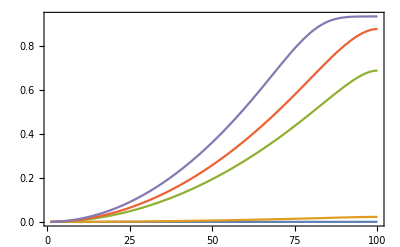

```mathematica
With[
{Δ=10,zIR=100},
Show[
Plot[Evaluate[a01[z,#,Δ,zIR]&/@{0.1,1,10,20,100}],{z,1,zIR},Frame->True]
]
]
```

So far the normalization have not been included

```mathematica
aNormalization[σ0_,Δ_,zIR_:10^8,g_:1]:=zIR/σ0/Sqrt[
Δ^2/((-1+Δ) Gamma[-1/Δ]^2) HypergeometricPFQ[{1/2-1/Δ},{1-2/Δ,2-1/Δ},((g σ0)/Δ)^2]+
Δ^4/((-1+2 Δ)(Δ-1)^2 Gamma[-1/Δ]^2) ((g σ0)/(2Δ))^2 HypergeometricPFQ[{3/2-1/Δ},{3-2/Δ,3-1/Δ},((g σ0)/Δ)^2]+
(Δ-1)/(Δ Gamma[1/Δ] Gamma[-1/Δ]) ((g σ0)/(2Δ))^(-2+2/Δ)BesselI[(Δ-1)/Δ,(g σ0)/Δ]/BesselI[-(Δ-1)/Δ,(g σ0)/Δ] (HypergeometricPFQ[{-1/2},{1-1/Δ,-1+1/Δ},((g σ0)/Δ)^2]-1)-
Sin[π/Δ]/(Δ^2 π) ((g σ0)/(2Δ))^(-2+2/Δ)BesselI[(Δ-1)/Δ,(g σ0)/Δ]/BesselI[-(Δ-1)/Δ,(g σ0)/Δ](HypergeometricPFQ[{-1/2},{-1/Δ,1/Δ},((g σ0)/Δ)^2]-1) +
1/(4(1+Δ)  Gamma[1/Δ]^2)((g σ0)/(2Δ))^(-2+4/Δ) (BesselI[(Δ-1)/Δ,(g σ0)/Δ]/BesselI[-(Δ-1)/Δ,(g σ0)/Δ])^2(4  (1+Δ) HypergeometricPFQ[{-1/2+1/Δ},{1+1/Δ,-1+2/Δ},((g σ0)/Δ)^2]+g^2 σ0^2  HypergeometricPFQ[{1/2+1/Δ},{2+1/Δ,1+2/Δ},((g σ0)/Δ)^2])
];
```

Check that the normalization used agree with actual value
n at σ0 = 10, Δ = 10 is 5.85648×10^7

```mathematica
aNormalization[10, 10]//N
```

5.85648×10^7

Visualize the difference between the exact, first order approximation (dashed), and current approximation (dot dashed)

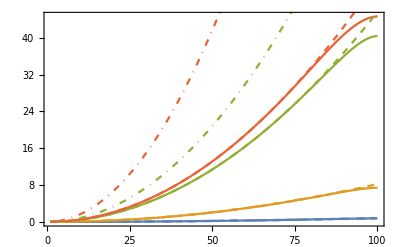

```mathematica
With[
{Δ=10,zIR=100},
Show[
Plot[Evaluate[(aNormalization[#,Δ,zIR]a01[z,#,Δ,zIR] )&/@{0.1,1,10,20}],{z,1,zIR},Frame->True],
Plot[Evaluate[(aNormalization[#,Δ,zIR]aApprox01[z,#,Δ,zIR])&/@{0.1,1,10,20}],{z,1,zIR},Frame->True,PlotStyle->Dashed],
Plot[Evaluate[(aApprox01Original[z,#,Δ,zIR] )&/@{0.1,1,10,20}],{z,1,zIR},Frame->True,PlotStyle->DotDashed]
]
]
```

#### Numerical overlap of the non-flat axion profile and fermion profiles

```mathematica
With[{cList={-2,-1,0},Δ=10,zIR=10^9,log10min=-2,log10max=2,log10step=0.05, Mpl=1.22 10^19},
tab=Log10[ Table[{σ0,1/Mpl aNormalization[σ0,Δ,zIR]NIntegrate[1/z^4 FermionProfile[c,z,zIR]^2 a01[z,σ0,Δ,zIR],{z,1.01,zIR}]},
{c,cList},{σ0,10^Range[log10min,log10max,log10step]}]]//Timing//Quiet;
tab2=Log10[Table[{σ0,1/Mpl aNormalization[σ0,Δ,zIR]NIntegrate[1/z^4 FermionProfile[c,z,zIR]^2 aApprox01[z,σ0,Δ,zIR],{z,1.01,zIR}]},
{c,cList},{σ0,10^Range[log10min,log10max,log10step]}]]//Timing//Quiet;
tab3=Log10[Table[{σ0,1/Mpl NIntegrate[1/z^4 FermionProfile[c,z,zIR]^2 aApprox01Original[z,σ0,Δ,zIR],{z,1.01,zIR}]},
{c,cList},{σ0,10^Range[log10min,log10max,log10step]}]]//Timing//Quiet
];
tab[[1]]
tab2[[1]]
tab3[[1]]
```

3.39063

2.125

1.73438

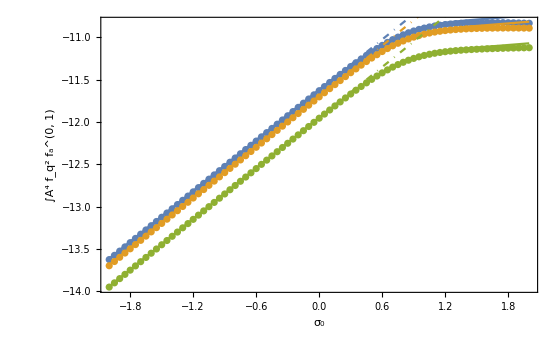

```mathematica
Show[
ListPlot[tab[[2]],Frame->True,FrameLabel->{"σ_0","∫A^4 f_q^2 f_a^(0, 1)"}],
ListPlot[tab2[[2]],Frame->True,FrameLabel->{"σ_0","∫A^4 f_q^2 f_a^(0, 1)"},Joined->True],
ListPlot[tab3[[2]],Frame->True,FrameLabel->{"σ_0","∫A^4 f_q^2 f_a^(0, 1)"},Joined->True,PlotStyle->DotDashed]
]
```

#### Approximate the overlap

These two expressions are committed to the package.

Note that for some loop over c, it is faster to calculate the non-normalized overlap first. Nonetheless, the approximate expression is a few time faster than doing the numerical integral.

```mathematica
With[{cList={-2,-1,0},Δ=10,zIR=10^9,log10min=-2,log10max=2,log10step=0.05,Mpl=1.22 10^19},
tab4= Table[Log10[{σ0,1/Mpl FermionAxionOverlap2[c,Δ,σ0,zIR]}],
{c,cList},{σ0,10^Range[log10min,log10max,log10step]}]//Timing//Quiet;
]
tab4[[1]]
```

0.75

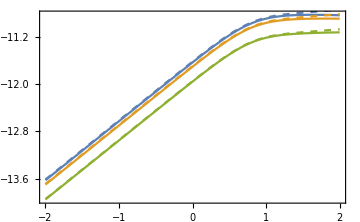

```mathematica
fig = Show[
ListPlot[tab[[2]],
Joined->True,
Frame->True,FrameLabel->{MaTeX["\sigma_0"],MaTeX["\int A^4 f_q^2 \widehat{f}_a^{(0)}"]},
ImageSize->Medium],
ListPlot[tab4[[2]],
Joined->True,
PlotStyle->Dashed]
]
```

```mathematica
With[{cList=Range[-4,0,1],Δ=10,Fa = 1. 10^9,log10min=-2,log10max=2,log10step=0.05, Mpl=1.22 10^19},
logσ0List=Range[log10min,log10max,log10step];
length = Length[logσ0List];
zIRList=10^logσ0List/Sqrt[Δ-1] Mpl/Fa;
tab5=Table[{logσ0List[[i]],Log10[1/zIRList[[i]] aNormalization[10^(logσ0List[[i]]),Δ,zIRList[[i]]]NIntegrate[1/z^4 FermionProfile[c,z,zIRList[[i]]]^2 a01[z,10^(logσ0List[[i]]),Δ,zIRList[[i]]],{z,1.01,zIRList[[i]]}]]},
{c,cList},{i,length}]//Timing//Quiet;
tab6=Table[{logσ0List[[i]],Log10[1/zIRList[[i]] NIntegrate[1/z^4 FermionProfile[c,z,zIRList[[i]]]^2 aApprox01Original[z,10^logσ0List[[i]],Δ,zIRList[[i]]],{z,1.01,zIRList[[i]]}]
]},
{c,cList},{i,length}]//Timing//Quiet;
]
```

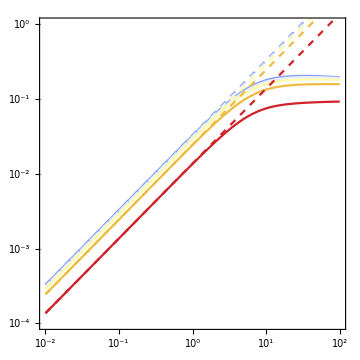

```mathematica
l = Length[tab5[[2]]];
SetOptions[ListPlot,{Joined->True,Frame->True,Axes->False}];
fig = Show[
ListPlot[tab5[[2]],
ImageSize->Medium,AspectRatio->1,
PlotStyle->Table[ColorData["TemperatureMap"][i/(l)],{i,l}],
FrameLabel->{MaTeX["\sigma_0"],MaTeX["\int dz \, A^4 \widehat{f}_z^{(0)} f_j^2 "]},
PlotRange->{{-2,2},{-4,0}},
FrameTicks->{
{LogTicks[10,-6,2],LogTicks[10,-6,2,ShowTickLabels->False]},
{LogTicks[10,-2,2],LogTicks[10,-2,2,ShowTickLabels->False]}
}
],
ListPlot[tab6[[2]],
PlotStyle->({#,Dashed}&/@Table[ColorData["TemperatureMap"][i/(l)],{i,l}])]
]
```

```mathematica
Export["Figures/axion_quark_overlap.pdf",fig]
```

Figures/axion_quark_overlap.pdf